## Calculating Phase Matching Conditions; Everything starts with the Sellmeier Equations. This is for the collinear regime. Assuming monochromatic pump, uniaxial crystals and an infinitely large crystal.

Sellmeier Equations for BBO

```mathematica
<<"ErrorBarPlots`"
Off[General::"spell1"]
Off[General::"spell"]
Off[General::"pspec"]
ordindex[λ_]:=√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ);
extindex[λ_]:=√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ);
airindex[λ_]:=1.000287566+1.3412/((10^18 (λ λ))/10^12);
```

Refractive indices for pump and degenerate wavelength in BBO

```mathematica
BB=ordindex[0.405]^2
CC=extindex[0.405]^2 
AA=ordindex[0.81]^2
DD=extindex[0.81]^2
```

2.86248

2.45588

2.75646

2.3845

Angle of Optical Axis to Pump Wave Vector for Degenerate Collinear Phase Matching

```mathematica
Θ=ArcCos[Sqrt[(CC/AA -1)*(BB/(CC-BB))]]*180/π
```

28.8159

Calculating non-degenerate uses a slightly more complicated equation

```mathematica
λp=0.405;
λs=0.76;λi=λs*λp/(λs-λp)
nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];nairi=airindex[λi];nairs=airindex[λs];
Θ=ArcCos[Sqrt[(λs^2*λi^2/(λp^2*(λi*nos +λs*noi)^2) -1/nep^2)*(nop^2*nep^2)/(nep^2-nop^2)]]*180/π
(*after crystal*)
```

0.867042

28.7591

## Lateral Walkoff Calculation for Pump

```mathematica
15.76Tan[ArcTan[(BB/CC) Tan[Θ]]-Θ]
```

1.03855

## Lateral Walkoff Calculation for SPDC

```mathematica
15.76Tan[ArcTan[(nos/nes)^2Tan[Θ]]-Θ]
```

0.982314

Calculating the angles needed to get a particular wavelength to be collinear. We also plot the results.

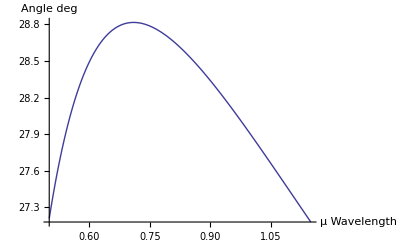

```mathematica
thetafinder[incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei},λp=0.405;λs=0.6+incre 0.0005;λi=(λs λp)/(λs-λp);nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];theta=(ArcCos[√((((λs^2 λi^2)/(λp^2 (λi nos+λs noi)^2)-1/nep^2) (nop^2 nep^2))/(nep^2-nop^2))] 180)/π;Return[theta];]
WAVELENGTHLIMIT=1300;
Clear[thetalist,index];
thetalist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,thetalist⟦index⟧=thetafinder[index];index++;];
DataTable=Table[{0.5+i 0.0005,thetalist⟦i⟧},{i,WAVELENGTHLIMIT}];
ListPlot[DataTable,AxesLabel->{Wavelength μ,Angle deg},Joined->True]
```

we can also calculate the emission angles of different wavelengths when we fix the angle between the pump and Optical axis of the crystal.

```mathematica
Clear[a,b,c,d,e,x,λs,λi,λp,nos,noi,nop,nes,nei,nep,Θs,Θp];
λp=0.405;λs=0.78;λi=λs*λp/(λs-λp);
c=2.989*10^8;
ωp=2*π*c*100000/λp;ωs=2*π*c*100000/λs;ωi=2*π*c*100000/λi;
Θp=28.5*π/180;
nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];
nei=extindex[λi];nairi=airindex[λi];nairs=airindex[λs];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
a=npeff*ωp/(noi*ωi);
b=nos*ωs/(noi*ωi);
c=nos;
d=nos*nos + (ωp*npeff/ωs)^2;
e=2*ωp*npeff*nos/ωs;
SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];
corr=x/.SolnList[[1]];
corr=If[corr<1,corr,1];
ArcCos[corr]*180/π;
(*after entering air*)
ArcSin[Sin[ArcCos[corr]]*noi/nairi]*180/π
SolnList
```

0.

{{x→1.0004},{x→1.45914},{x→2.48035}}

```mathematica
(*emissionfinder gives the exit angles after the crystal, negemission finder gives the emission angles inside the crystal*)
```

0

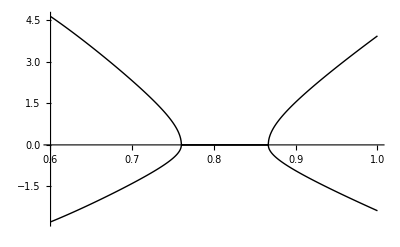

```mathematica
emissionfinder[incangle_,incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei,npeff,Θp,ωp,ωs,ωi,a,b,c,d,e,SolnList,corr},λp=0.405;λs=0.6+incre 0.0005;λi=(λs λp)/(λs-λp);c=2.989 10^8;ωp=(2 π c 100000)/λp;ωs=(2 π c 100000)/λs;ωi=(2 π c 100000)/λi;Θp=(incangle π)/180;nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];npeff=√(1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2));nairi=airindex[λi];nairs=airindex[λs];a=(npeff ωp)/(noi ωi);b=(nos ωs)/(noi ωi);c=nos;d=nos nos+((ωp npeff)/ωs)^2;e=(2 ωp npeff nos)/ωs;SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];corr=x/.SolnList⟦1⟧;corr=If[corr<1,corr,1];theta=(ArcCos[corr] 180)/π;theta=(Sin[ArcCos[corr]] nos 180)/(nairs π);Return[theta];];
negemissionfinder[incangle_,incre_]:=Module[{theta,λp,λs,λi,nop,nep,nos,nes,noi,nei,npeff,Θp,ωp,ωs,ωi,a,b,c,d,e,SolnList,corr},λp=0.405;λs=0.6+incre 0.0005;λi=(λs λp)/(λs-λp);c=2.989 10^8;ωp=(2 π c 100000)/λp;ωs=(2 π c 100000)/λs;ωi=(2 π c 100000)/λi;Θp=(incangle π)/180;nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];npeff=√(1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2));a=(npeff ωp)/(noi ωi);b=(nos ωs)/(noi ωi);c=nos;d=nos nos+((ωp npeff)/ωs)^2;e=(2 ωp npeff nos)/ωs;SolnList=NSolve[c-d+a^2 d-2 a b d x+e x-a^2 e x-c x^2+b^2 d x^2+2 a b e x^2-b^2 e x^3==0,x];corr=x/.SolnList⟦1⟧;corr=If[corr<1,corr,1];theta=-(ArcCos[corr] 180)/π;Return[theta];];
negemissionfinder[0,1]
WAVELENGTHLIMIT=800;
Clear[thetalist,negthetalist,index,incangle];
thetalist=Table[0,{i,WAVELENGTHLIMIT}];
negthetalist=Table[0,{i,WAVELENGTHLIMIT}];
incangle=28.76;
For[index=1,index<WAVELENGTHLIMIT+1,thetalist⟦index⟧=emissionfinder[incangle,index];index++;];
DataTable=Table[{0.6+i 0.0005,thetalist⟦i⟧},{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,negthetalist⟦index⟧=negemissionfinder[incangle,index];index++;];
DataTable1=Table[{0.6+i 0.0005,negthetalist⟦i⟧},{i,WAVELENGTHLIMIT}];
(*ListPlot[{DataTable,DataTable1},AxesLabel->{Wavelength μ,EmissionAngle deg}];*)
ListPlot[{DataTable,DataTable1},Joined->True,PlotStyle->Black]
```

For finding phase mismatch using the Boeuf argument

```mathematica
FindRoot[(Sin[x]/x)^2== 0.5,{x,0.3}]
```

{x→1.39156}

Finding Phase Matching, given the emission parameters. This shows the phase matching function as you vary the

0.682476

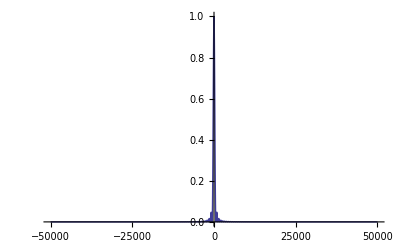

```mathematica
λp=0.4095;λs=0.7022;λi=λs*λp/(λs-λp);c=2.989*10^8;
ωp=2*π*c*1000000/λp;ωs=2*π*c*1000000/λs;ωi=2*π*c*1000000/λi;
nop=ordindex[λp];nep=extindex[λp];npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
Θp=28.5*π/180;Θi=0.0*π/180;Θs=Θi;
L=200; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(-nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2
Plot[Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2,{L,-50000,50000},PlotRange->{0,1}]
```

here we look at the spectrum of emission light that is collected for a given acceptance angle of our optical fibre.  We can choose
not to sum and look at the spectrum of emission along a single emission angle.

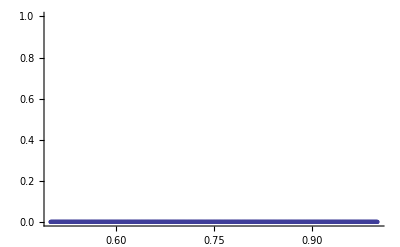

```mathematica
Clear[phasevaluelist,index];
phasematchcount[thetas_,ωp_,ωs_,ωi_,noi_,nos_,c_]:=Module[
{Θp,Θs,Θi,L,W,δkz,δky,δkx,npeff},
 Θp=15*π/180;
Θs=thetas*π/180;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=2000; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(-nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi])/(c*1000000);*)
Return[Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2];
];

phasevaluefinder[incre_]:=Module[
{phasevalue,λp,λs,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θs,dΘs},
λp=0.4095;λs=0.5+ incre*0.0005;λi=λs*λp/(λs-λp);c=2.989*10^8;
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
       ωp=2*π*c*1000000/λp;ωs=2*π*c*1000000/λs;ωi=2*π*c*1000000/λi;
       phasevalue=0;
dΘs=0.005;
       For[Θs=0,Θs<dΘs,Θs+=dΘs,phasevalue=phasematchcount[Θs,ωp,ωs,ωi,noi,nos,c]];
Return[phasevalue];
];
WAVELENGTHLIMIT=1000;
Clear[phasevaluelist];
phasevaluelist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,index++,phasevaluelist[[index]]=phasevaluefinder[index]];
PhaseDataTable=Table[{0.5+i*0.0005,phasevaluelist[[i]]},{i,WAVELENGTHLIMIT}];
ListPlot[PhaseDataTable,PlotRange->{0,1}]
```

```mathematica
SetDirectory["Z:\misc\alexstuff"];
Export["fwhm.dat",PhaseDataTable]
```

SetDirectory::cdir: Cannot set current directory to Z:\misc\alexstuff.

fwhm.dat

here we do numerical integration

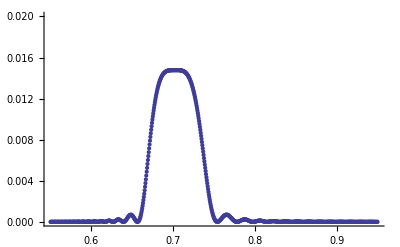

```mathematica
Clear[phasevaluelist,index];
phasematchcount[thetas_,ωp_,ωs_,ωi_,noi_,nos_,c_]:=Module[
{Θp,Θs,Θi,L,W,δkz,δky,δkx,npeff},
 Θp=33.5327*π/180;
Θs=thetas*π/180;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=2000; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(-nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);

(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi])/(c*1000000);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi])/(c*1000000);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi])/(c*1000000);*)
Return[Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2];
];

phasevaluefinder[incre_]:=Module[
{phasevalue,λp,λs,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θs,dΘs},
λp=0.3511;λs=0.55+ incre*0.0005;λi=λs*λp/(λs-λp);c=2.989*10^8;
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
       ωp=2*π*c*1000000/λp;ωs=2*π*c*1000000/λs;ωi=2*π*c*1000000/λi;
       phasevalue=0;
dΘs=0.005;
       For[Θs=-dΘs,Θs<=dΘs,Θs+=dΘs,phasevalue+=phasematchcount[Θs,ωp,ωs,ωi,noi,nos,c]*dΘs];

Return[phasevalue];
];
WAVELENGTHLIMIT=800;
Clear[phasevaluelist];
phasevaluelist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,index++,phasevaluelist[[index]]=phasevaluefinder[index]];
PhaseDataTable=Table[{0.55+i*0.0005,phasevaluelist[[i]]},{i,WAVELENGTHLIMIT}];
ListPlot[PhaseDataTable,PlotRange->{0,0.02}]
```

```mathematica
SetDirectory["Z:\misc\alexstuff"];
Export["fwhm.dat",PhaseDataTable]
```

SetDirectory::cdir: Cannot set current directory to Z:\misc\alexstuff.

fwhm.dat

here we attempt to do 3D plotting. Plot the Phase Matching Function at an emission angle and wavelength

```mathematica
<<"BarCharts`";<<"Histograms`"
Clear[phasevaluelist,index];
phasematchcount[thetas_,ωp_,ωs_,ωi_,noi_,nos_,c_,λs_]:=Module[{Θp,Θs,Θi,L,W,δkz,δky,δkx,npeff,phasedatatable,Φ},Θp=(33.5327 π)/180;Θs=(thetas π)/180;Θi=ArcSin[(nos ωs Sin[Θs])/(noi ωi)];npeff=√(1/((Cos[Θp]/nop)^2+(Sin[Θp]/nep)^2));L=2000;W=82;δkz=(npeff ωp-nos ωs Cos[Θs]-noi ωi Cos[Θi])/(c 1000000);δkx=0;δky=(-nos ωs Sin[Θs]+noi ωi Sin[Θi])/(c 1000000);phasedatatable=Table[0,{i,3}];Φ=ⅇ^(1/2 (-W^2) (δkx^2+δky^2)) (Sin[(δkz L)/2]/((δkz L)/2))^2;phasedatatable⟦1⟧=λs;phasedatatable⟦2⟧=thetas;phasedatatable⟦3⟧=Φ;Return[phasedatatable];];
phasevaluefinder[incre_]:=Module[{phasevalue,λp,λs,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θs,dΘs},λp=0.3511;λs=0.55+incre 0.0005;λi=(λs λp)/(λs-λp);c=2.989 10^8;nop=ordindex[λp];nep=extindex[λp];nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];ωp=(2 π c 1000000)/λp;ωs=(2 π c 1000000)/λs;ωi=(2 π c 1000000)/λi;dΘs=0.05;startangle=-0.1;endangle=0.1;phasevalue=Table[0,{i,(endangle-(startangle-dΘs))/dΘs}];For[Θs=startangle,Θs≤endangle,Θs+=dΘs,phasevalue⟦(Θs-startangle+dΘs)/dΘs⟧=phasematchcount[Θs,ωp,ωs,ωi,noi,nos,c,λs]];Return[phasevalue];];
WAVELENGTHLIMIT=800;
Clear[phasevaluelist];
phasevaluelist=Table[0,{i,WAVELENGTHLIMIT}];
For[index=1,index<WAVELENGTHLIMIT+1,index++,phasevaluelist⟦index⟧=phasevaluefinder[index]];
```

General::obspkg: BarCharts` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

BarChart3D::shdw: Symbol BarChart3D appears in multiple contexts BarCharts`System`; definitions in context BarCharts` may shadow or be shadowed by other definitions.

General::obspkg: Histograms` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

Histogram3D::shdw: Symbol Histogram3D appears in multiple contexts Histograms`System`; definitions in context Histograms` may shadow or be shadowed by other definitions.

here we calculate the phase function against emission angle, fixing other quantities

```mathematica
phasefunction[thetas_,λs_]:=Module[
{Φ,λp,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θp,Θs,Θi,L,W,δkz,δky,δkx},
λp=0.3511;λi=λs*λp/(λs-λp);
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
Θp=33.327*π/180;
Θs=thetas*π/180;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
ωp=2*π/λp;ωs=2*π/λs;ωi=2*π/λi;
       npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=2000; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs] + noi*ωi*Sin[Θi]);

(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi]);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi]);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi]);*)
Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2;
Return[Φ];
];
```

```mathematica
ListDensityPlot[Table[phasefunction[x,y],{x,-2,2,0.05},{y,0.5,0.9,0.001}],Mesh->False,PlotRange->{0,1}]
```

-Graphics-

here we calculate the phase function against exit angle, fixing other quantities

```mathematica
phasefunction[thetas_,λs_]:=Module[
{Φ,λp,λi,c,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θp,Θs,Θi,L,W,δkz,δky,δkx},
λp=0.3511;λi=λs*λp/(λs-λp);
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];nairi=airindex[λi];nairs=airindex[λs];
Θp=33.327*π/180;
Θs=ArcSin[Sin[thetas*π/180]*nairs/nos];(*emissionangle inside the crystal*)
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
ωp=2*π/λp;ωs=2*π/λs;ωi=2*π/λi;
       npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=2000; (*length of crystal*)
W=82;(*waist of pump *)
δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs] + noi*ωi*Sin[Θi]);
(*
δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi]);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi]);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi]);
*)
Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2;
Return[Φ];
];
```

```mathematica
ListDensityPlot[Table[phasefunction[x,y],{x,-2,2,0.05},{y,0.5,0.9,0.001}],Mesh->False,PlotRange->{0,1}]
```

-Graphics-

```mathematica
(*ListPlot3D[Table[phasefunction[x,y],{y,0.55,0.9,0.001},{x,-1,1,0.05}],Mesh->False,PlotRange->{0,1},AxesLabel->{"Emission Angle","Wavelength","PhaseFunction"},Axes->True,ViewPoint->{0,0,1}]*)
```

Coincidence Spectrum given two pump lines; and collinear emission

```mathematica
pumpenv[λs_,λi_,Λp_] := Module[
{σp,ans},
σp=0.001*(Λp*Λp);
ans=-(1/λs+1/λi-1/Λp)^2/σp^2;
If[ans<-300,ans=-∞];
Return[Exp[ans]^2];
];
jointphasefunction[λs_,λi_]:=Module[
{Φ,λp,nop,nep,nos,nes,noi,nei,npeff,ωp,ωs,ωi,Θp,Θs,Θi,L,W,δkz,δky,δkx},
Θp=33.5327*π/180;
Θs=0;
Θi=ArcSin[nos*ωs*Sin[Θs]/(noi*ωi)];
λp=0.3511;
nop=ordindex[λp];nep=extindex[λp];
nos=ordindex[λs];nes=extindex[λs];noi=ordindex[λi];nei=extindex[λi];
       ωp=2*π/λp;ωs=2*π/λs;ωi=2*π/λi;
       npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];
L=2000; (*length of crystal*)
W=82;(*waist of pump *)

δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs] + noi*ωi*Sin[Θi]);

(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi]);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi]);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi]);*)
Φ=Exp[-W^2(δkx^2 + δky^2)/2]*(Sin[δkz*L/2]/(δkz*L/2))^2*pumpenv[λs,λi,λp];
λp=0.3514;
nop=ordindex[λp];nep=extindex[λp];
ωp=2*π/λp;
       npeff=Sqrt[1/((Cos[Θp]/nop)^2 + (Sin[Θp]/nep)^2)];

δkz=(npeff*ωp -nos*ωs*Cos[Θs] - noi*ωi*Cos[Θi]);
δkx=0;
δky=(-nos*ωs*Sin[Θs] + noi*ωi*Sin[Θi]);

(*δkz=(npeff*ωp*Cos[Θp] -nos*ωs*Cos[Θp]*Cos[Θs] - noi*ωi*Cos[Θp]*Cos[Θi]);
δkx=(nos*ωs*Sin[Θs] - noi*ωi*Sin[Θi]);
δky=(npeff*ωp*Sin[Θp] -nos*ωs*Sin[Θp]*Cos[Θs] - noi*ωi*Sin[Θp]*Cos[Θi]);
*)
Φ+=Exp[-W^2(δkx^2 + δky^2)/2](Sin[δkz*L/2]/(δkz*L/2))^2*pumpenv[λs,λi,λp];
(*If[Φ<0.00000000000001,Φ=0];*)
Return[Φ];
];
(*Timing[gr3=DensityGraphics[Table[jointphasefunction[x,y],{x,0.65,0.75,0.0005},{y,0.65,0.75,0.0005}],Mesh->False,PlotRange->{0,1}]]
Show[gr3]*)
```

0.0154679

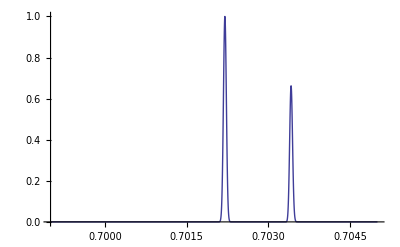

```mathematica
phasefunction[0,0.7022]
Plot[jointphasefunction[x,0.7022],{x,0.699,0.705},PlotRange->{0,1}]
```

```mathematica
kxs=nos*ωs*Sin[Θs] ;kys=nos*ωs*Sin[Θp]*Cos[Θs];
kxi=-noi*ωi*Sin[Θi];kyi=noi*ωi*Sin[Θp]*Cos[Θi];

Θ=-0.18*π/360;kpps1=kxs^2 + kys^2;
Θ=0.18*π/360;kpps2=kxs^2 + kys^2;
(82*kpps1 + 82*kpps2)/82
```

1.20711×10^31